## LSTM

```mathematica
rescaledSubtractedTS=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\rescaledsubtractedTS.wxf"];
```

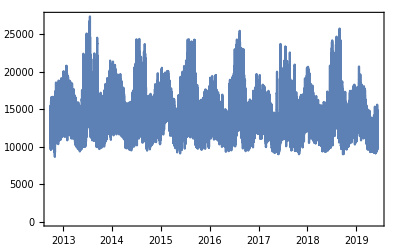

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
data=rescaledSubtractedTS//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,10,1];valuesp = values[[10;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,10}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
58680
```

```mathematica
Length@threaddata
```

57680

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
trainingdata[[;;1]]
```

{{{0.159085,0.118562,0.10918,0.106807,0.104909,0.116728,0.152632,0.225146,0.289792,0.319685}}→0.319685}

```mathematica
columnHeads
```

```mathematica
mldata
```

$Aborted[]

```mathematica
rnn=NetChain[{
	LongShortTermMemoryLayer[20],
	LinearLayer[100],
	ElementwiseLayer[Ramp],
	60,
	Ramp,
	50,
	Ramp,1}]
```

NetChain[<>]

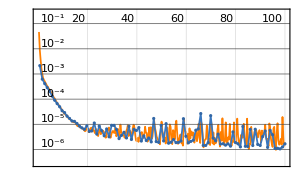
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:43s  examples/s:107647
data | ,,  training examples:45000  validation examples:13671  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.23×10^-6
validation | ,,  loss:1.67×10^-6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainednet=NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→0.00111665|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{0.369093,0.37334,0.367965,0.35475,0.343098,0.338917,0.340734,0.358589,0.384605,0.397505}}→0.397505,{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144}}→0.250144}

```mathematica
trainednet[rsample[[2,1]]]
```

NetTrain Results
summary | ,,  batches:5700  rounds:100  time:43s  examples/s:107647
data | ,,  training examples:45000  validation examples:13671  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.23×10^-6
validation | ,,  loss:1.67×10^-6
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144}}]

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
tvalues=Table[trainednet[testdata[[i,1]]],{i,1,Length@testdata}]
```

$Aborted[]

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainednet[#]}],1]&,testdata[[1,1]],100]
```

$Aborted[]

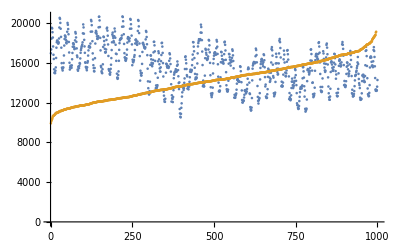

```mathematica
ListPlot[{testdata[[1;;1000,2]],results}]
```